```mathematica
(* Fixed alpha and pi_r, nondimensionalization wrt w*)
(* SAMPLED quantities *)

xi[lambda_]:=1-Exp[-lambda];
cks[a_,r_,lambda_,k_,eta_]:=a/r/k!*(eta*xi[lambda]*r/(1-(1-eta)*xi[lambda]*r))^k*((1-xi[lambda]*r)/(1-(1-eta)*xi[lambda]*r))^(a/r)*Product[a/r+j,{j,1,k-1}];
cksave[a_,lambda_,k_,eta_]:=NIntegrate[cks[a,r,lambda,k,eta],{r,0,1}];
cksavez[a_,lambda_,k_,eta_]:=NIntegrate[cks[a,1-Exp[-z],lambda,k,eta]*Exp[-z],{z,0,30}];

cksmu[a_,r_,mu_,k_,eta_]:=a/r/k!*(eta*r/mu/(1-(1-eta)*r/mu))^k*((1-r/mu)/(1-(1-eta)*r/mu))^(a/r)*Product[a/r+j,{j,1,k-1}];

CT[a_,lambda_,eta_]:=NIntegrate[(1-((1-r*xi[lambda])/(1-(1-eta)*xi[lambda]*r))^(a/r)),{r,0,1}]

(*  Plot3D[CT[a,lambda,0.001],{a,1,100},{lambda,1,10}] *)
```

```mathematica
(* a_bar = 0.1, lambda = 10 *)
Do[Print[k,"   ",cksave[0.1,10,k,0.0001],"   ",cksave[0.1,10,k,0.0001]/CT[0.1,10,0.0001],"   ",k*cksave[0.1,10,k,0.0001]/CT[0.1,10,0.0001]],{k,1,10}]
```

1   0.000087523   0.945887   0.945887

2   3.6062×10^-6   0.0389733   0.0779466

3   8.52826×10^-7   0.00921674   0.0276502

4   2.9992×10^-7   0.00324132   0.0129653

5   1.26005×10^-7   0.00136178   0.00680888

6   5.86494×10^-8   0.000633841   0.00380304

7   2.91878×10^-8   0.000315441   0.00220809

8   1.52284×10^-8   0.000164578   0.00131662

9   8.22952×10^-9   0.0000889388   0.000800449

10   4.56989×10^-9   0.0000493881   0.000493881

```mathematica
(* Data beta chain of CD4 *)
```

```mathematica
fks[a_,lambda_,k_,eta_]:=k*cksave[a,lambda,k,eta]/a/lambda/eta

fkd={0.8748166656414875,0.10961857671109042,0.012633603541157418,0.0019672764638298573,0.00042814610540939987,0.0002371270737652059,6.147738949468303*10^(-5),3.51299368541045*10^(-5),7.904235792173532*10^(-5),2.1956210533815365*10^(-5),7.245549476159072*10^(-5),0.0,2.8543073693959976*10^(-5)};
```

```mathematica
error[a_,lambda_,eta_]:=Sum[(fks[a,lambda,k,0.0001]-fkd[[k]])^2,{k,1,13}]
Do[Print[lambda,"  ",error[0.1,lambda,0.0001]],{lambda,5,15,0.5}]
```

5.  0.030337

5.5  0.0295685

6.  0.0284302

6.5  0.0267716

7.  0.0244216

7.5  0.0212381

8.  0.0172095

8.5  0.0125939

9.  0.00800635

9.5  0.00432168

10.  0.00237702

10.5  0.00267021

11.  0.00527004

11.5  0.0099339

12.  0.0162878

12.5  0.023959

13.  0.0326305

13.5  0.0420448

14.  0.0519937

14.5  0.0623088

15.  0.0728547

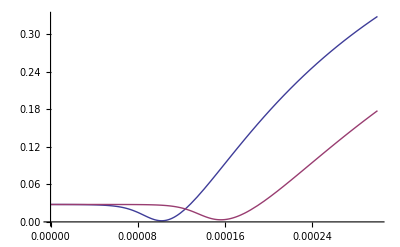

```mathematica
(* energy landscape has a curve of near minimum *)
Plot[{Sum[(fks[0.00001,sigma/0.00001,k,0.0001]-fkd[[k]])^2,{k,1,13}],Sum[(fks[0.00001,sigma/0.00001,k,0.000001]-fkd[[k]])^2,{k,1,13}]},{sigma,0,0.0003}]
```

```mathematica
sigma/.FindMinimum[Sum[(fks[10^(-3),sigma/(10^(-3)),k,0.0001]-fkd[[k]])^2,{k,1,13}],{sigma,0.02}][[2]]
```

NIntegrate::inumr: The integrand 1.×10^-7\ (1 - ⅇ^-1000\ sigma)\ (1 - (1 - Power[« 2 »])\ r/1 - 0.9999\ (1 + Times[« 2 »])\ r)^1/1000\ r/1 - 0.9999\ (1 - ⅇ^Times[« 2 »])\ r has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

0.0101937

```mathematica
Do[Print[10^a,"  ",FindMinimum[Sum[(fks[10^a,sigma/(10^a),k,0.0001]-fkd[[k]])^2,{k,1,13}],{sigma,0.00001}]],{a,-5,-2,0.1}]
```

NIntegrate::inumr: The integrand 1.×10^-9\ (1 - ⅇ^-100000.\ sigma)\ (1 - (1 - Power[« 2 »])\ r/1 - 0.9999\ (1 + Times[« 2 »])\ r)^0.00001/r/1 - 0.9999\ (1 - ⅇ^Times[« 2 »])\ r has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

0.00001  {0.00182891,{sigma→0.000101953}}

0.0000125893  {0.00182891,{sigma→0.000128351}}

0.0000158489  {0.00182891,{sigma→0.000161584}}

0.0000199526  {0.0018289,{sigma→0.000203422}}

0.0000251189  {0.00182889,{sigma→0.000256093}}

0.0000316228  {0.00182889,{sigma→0.000322401}}

0.0000398107  {0.00182888,{sigma→0.000405879}}

0.0000501187  {0.00182886,{sigma→0.00051097}}

0.0000630957  {0.00182885,{sigma→0.000643272}}

0.0000794328  {0.00182883,{sigma→0.00080983}}

0.0001  {0.0018288,{sigma→0.00101951}}

0.000125893  {0.00182877,{sigma→0.00128348}}

0.000158489  {0.00182873,{sigma→0.0016158}}

0.000199526  {0.00182868,{sigma→0.00203416}}

0.000251189  {0.00182862,{sigma→0.00256084}}

0.000316228  {0.00182854,{sigma→0.00322387}}

0.000398107  {0.00182844,{sigma→0.00405856}}

0.000501187  {0.00182831,{sigma→0.00510935}}

0.000630957  {0.00182815,{sigma→0.00643216}}

0.000794328  {0.00182795,{sigma→0.0080974}}

0.001  {0.0018277,{sigma→0.0101937}}

0.00125893  {0.00182739,{sigma→0.0128326}}

0.00158489  {0.00182699,{sigma→0.0161545}}

0.00199526  {0.00182649,{sigma→0.020336}}

0.00251189  {0.00182586,{sigma→0.0255995}}

0.00316228  {0.00182507,{sigma→0.0322246}}

0.00398107  {0.00182407,{sigma→0.0405632}}

0.00501187  {0.00182282,{sigma→0.051058}}

0.00630957  {0.00182125,{sigma→0.0642654}}

0.00794328  {0.00181928,{sigma→0.0808851}}

0.01  {0.0018168,{sigma→0.101796}}

```mathematica
Do[Print[k,"  ",fks[141.316,3.74818,k,0.0001],"   ",fkd[[k]]],{k,1,13}]
```

1  0.866979   0.865832

2  0.117732   0.116938

3  0.0166051   0.0142497

4  0.0021389   0.00194254

5  0.000238773   0.000465676

6  0.0000231416   0.000199576

7  1.97197×10^-6   0.0000931353

8  1.49709×10^-7   0.

9  1.0246×10^-8   0.000119745

10  6.38549×10^-10   0.

11  3.65508×10^-11   0.0000731777

12  1.93571×10^-12   0.

13  9.54446×10^-14   0.0000864827